Datos salida\quadavg_26-04-24_3500_5.csv_output.csv

42

FittedModel[…]

| Estimate | Standard Error | t-Statistic | P-Value
RPMs | 4157.45 | 32.6341 | 127.396 | 6.63208×10^-55

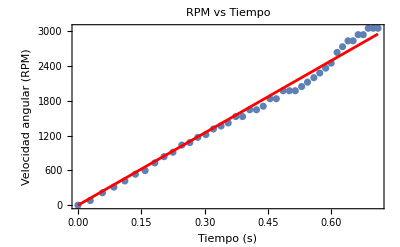

```mathematica
notebookDirectory = NotebookDirectory[];
fileName = "Datos salida\\quadavg_26-04-24_3500_5.csv_output.csv"
fullPath = StringJoin[{notebookDirectory, fileName}];

data = Import[fullPath, "Data"];
data = data[[2;;]];
seconds = data[[All, 1]];
Length[seconds]
seconds = MapAt[# - seconds[[1]] &, seconds, All];
voltage = data[[All, 3]];
voltage = MapAt[# - voltage[[1]] &, voltage, All];
data = Transpose[{seconds,voltage}];
dataPlot = ListPlot[data];

(*y-intercept is set zero.*)
fitModel = NonlinearModelFit[data, RPMs x, RPMs, x]
fitModel["ParameterTable"]

modelPlot = Plot[fitModel[x], {x, Min[data[[All, 1]]], Max[data[[All, 1]]]}, PlotStyle->Red];

Show[dataPlot, modelPlot, PlotLabel->"RPM vs Tiempo", Frame->True, FrameLabel->{"Tiempo (s)", "Velocidad angular (RPM)"}]
```